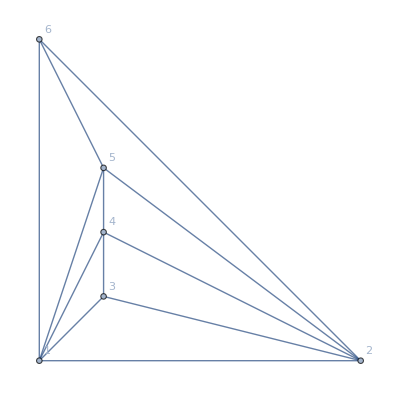

```mathematica
MinimalGraph[5]
```

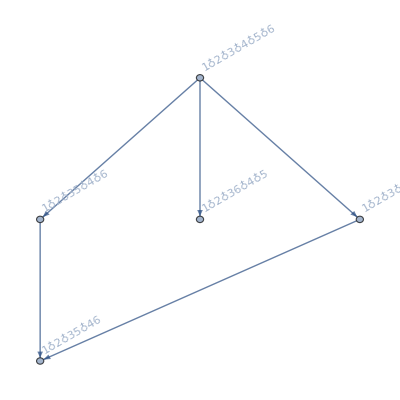

```mathematica
FormulaGraphReverse2[FindFullFormula[MinimalGraph[5]]]
```

```mathematica
nodes=With[{g=MinimalGraph[5]},
With [{full=FindFullFormula[g]},
Table[ImpliedNodes[Map[SymbolReplace[#,e]&,FindFullFormula[EdgeContract[g,e]]],full],{e,EdgeList[g]}]
]
]//Flatten//Tally
```

{{v1x2x3x4x5x6,12},{v1x2x3x46x5,6},{v1x2x36x4x5,8},{v1x2x35x4x6,6},{v1x2x35x46,1}}

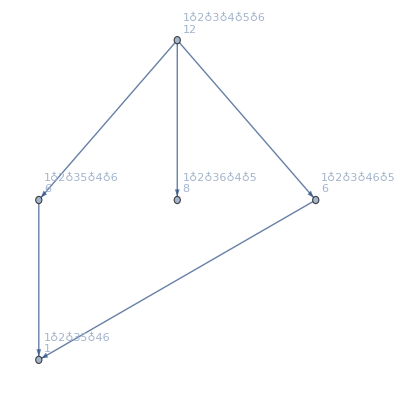

```mathematica
Block[{vert,graph},
vert=Map[First,nodes];
graph=Graph[FormulaGraphReverse2[vert],VertexLabels->Map[#[[1]]->Column[{SymbolToLabel[#[[1]]],Style[#[[2]],Red,Bold]},Center]&,nodes]];
graph
]
```

```mathematica
With[{g=MinimalGraph[5]},
With [{full=FindFullFormula[g]},
{FindFullFormula[EdgeContract[g,2<->3]],
full,
ImpliedNodes[FindFullFormula[EdgeContract[g,2<->3]],full]
}
]
]
```

{{v1x2x4x5x6,v1x2x46x5},{v1x2x3x4x5x6,v1x2x3x46x5,v1x2x36x4x5,v1x2x35x4x6,v1x2x35x46},{}}

```mathematica
DownSymbols[s_]:=Map[SetsToSymbol,FindCoarser[SymbolToSets[s]]];
```

```mathematica
DownSymbols[v1x2x3x4x5x6]
```

{v12x3x4x5x6,v13x2x4x5x6,v14x2x3x5x6,v15x2x3x4x6,v16x2x3x4x5,v1x23x4x5x6,v1x24x3x5x6,v1x25x3x4x6,v1x26x3x4x5,v1x2x34x5x6,v1x2x35x4x6,v1x2x36x4x5,v1x2x3x45x6,v1x2x3x46x5,v1x2x3x4x56}

```mathematica
UpSymbols[s_]:=Map[SetsToSymbol,FindFiner[SymbolToSets[s]]]
```

```mathematica
UpSymbols[v1x2x35x46]
```

{v1x2x3x46x5,v1x2x35x4x6}

```mathematica
CommonDownWards[symbols_]:=Block[{allDown={},result={}, up},
Table[
allDown=DeleteDuplicates[Join[allDown,DownSymbols[s]]],
{s,symbols}
];
Print[allDown];
allDown=DeleteDuplicates[allDown];
Table[
up=UpSymbols[down];
Print[down->up->SubsetQ[symbols,up]];
If[SubsetQ[symbols,up],AppendTo[result,down]]
,{down,allDown}
];
result
]
```

```mathematica
CommonDownWards[{v12x3x4x56x789,v1x2x34x56x789,v12x34x5x6x789}]
```

{v123x4x56x789,v124x3x56x789,v1256x3x4x789,v12789x3x4x56,v12x34x56x789,v12x356x4x789,v12x3789x4x56,v12x3x456x789,v12x3x4789x56,v12x3x4x56789,v134x2x56x789,v156x2x34x789,v1789x2x34x56,v1x234x56x789,v1x256x34x789,v1x2789x34x56,v1x2x3456x789,v1x2x34789x56,v1x2x34x56789,v1234x5x6x789,v125x34x6x789,v126x34x5x789,v12789x34x5x6,v12x345x6x789,v12x346x5x789,v12x34789x5x6,v12x34x5789x6,v12x34x5x6789}

v123x4x56x789→{v1x23x4x56x789,v12x3x4x56x789,v13x2x4x56x789,v123x4x5x6x789,v123x4x56x7x89,v123x4x56x78x9,v123x4x56x79x8}→False

v124x3x56x789→{v1x24x3x56x789,v12x3x4x56x789,v14x2x3x56x789,v124x3x5x6x789,v124x3x56x7x89,v124x3x56x78x9,v124x3x56x79x8}→False

v1256x3x4x789→{v1x256x3x4x789,v12x3x4x56x789,v156x2x3x4x789,v125x3x4x6x789,v16x25x3x4x789,v126x3x4x5x789,v15x26x3x4x789,v1256x3x4x7x89,v1256x3x4x78x9,v1256x3x4x79x8}→False

v12789x3x4x56→{v1x2789x3x4x56,v12x3x4x56x789,v1789x2x3x4x56,v127x3x4x56x89,v189x27x3x4x56,v1289x3x4x56x7,v17x289x3x4x56,v1278x3x4x56x9,v19x278x3x4x56,v129x3x4x56x78,v178x29x3x4x56,v1279x3x4x56x8,v18x279x3x4x56,v128x3x4x56x79,v179x28x3x4x56,v12789x3x4x5x6}→False

v12x34x56x789→{v1x2x34x56x789,v12x3x4x56x789,v12x34x5x6x789,v12x34x56x7x89,v12x34x56x78x9,v12x34x56x79x8}→False

v12x356x4x789→{v1x2x356x4x789,v12x3x4x56x789,v12x35x4x6x789,v12x36x4x5x789,v12x356x4x7x89,v12x356x4x78x9,v12x356x4x79x8}→False

v12x3789x4x56→{v1x2x3789x4x56,v12x3x4x56x789,v12x37x4x56x89,v12x389x4x56x7,v12x378x4x56x9,v12x39x4x56x78,v12x379x4x56x8,v12x38x4x56x79,v12x3789x4x5x6}→False

v12x3x456x789→{v1x2x3x456x789,v12x3x4x56x789,v12x3x45x6x789,v12x3x46x5x789,v12x3x456x7x89,v12x3x456x78x9,v12x3x456x79x8}→False

v12x3x4789x56→{v1x2x3x4789x56,v12x3x4x56x789,v12x3x47x56x89,v12x3x489x56x7,v12x3x478x56x9,v12x3x49x56x78,v12x3x479x56x8,v12x3x48x56x79,v12x3x4789x5x6}→False

v12x3x4x56789→{v1x2x3x4x56789,v12x3x4x5x6789,v12x3x4x56x789,v12x3x4x5789x6,v12x3x4x567x89,v12x3x4x589x67,v12x3x4x5689x7,v12x3x4x57x689,v12x3x4x5678x9,v12x3x4x59x678,v12x3x4x569x78,v12x3x4x578x69,v12x3x4x5679x8,v12x3x4x58x679,v12x3x4x568x79,v12x3x4x579x68}→False

v134x2x56x789→{v1x2x34x56x789,v13x2x4x56x789,v14x2x3x56x789,v134x2x5x6x789,v134x2x56x7x89,v134x2x56x78x9,v134x2x56x79x8}→False

v156x2x34x789→{v1x2x34x56x789,v15x2x34x6x789,v16x2x34x5x789,v156x2x3x4x789,v156x2x34x7x89,v156x2x34x78x9,v156x2x34x79x8}→False

v1789x2x34x56→{v1x2x34x56x789,v17x2x34x56x89,v189x2x34x56x7,v178x2x34x56x9,v19x2x34x56x78,v179x2x34x56x8,v18x2x34x56x79,v1789x2x3x4x56,v1789x2x34x5x6}→False

v1x234x56x789→{v1x2x34x56x789,v1x23x4x56x789,v1x24x3x56x789,v1x234x5x6x789,v1x234x56x7x89,v1x234x56x78x9,v1x234x56x79x8}→False

v1x256x34x789→{v1x2x34x56x789,v1x25x34x6x789,v1x26x34x5x789,v1x256x3x4x789,v1x256x34x7x89,v1x256x34x78x9,v1x256x34x79x8}→False

v1x2789x34x56→{v1x2x34x56x789,v1x27x34x56x89,v1x289x34x56x7,v1x278x34x56x9,v1x29x34x56x78,v1x279x34x56x8,v1x28x34x56x79,v1x2789x3x4x56,v1x2789x34x5x6}→False

v1x2x3456x789→{v1x2x3x456x789,v1x2x34x56x789,v1x2x356x4x789,v1x2x345x6x789,v1x2x36x45x789,v1x2x346x5x789,v1x2x35x46x789,v1x2x3456x7x89,v1x2x3456x78x9,v1x2x3456x79x8}→False

v1x2x34789x56→{v1x2x3x4789x56,v1x2x34x56x789,v1x2x3789x4x56,v1x2x347x56x89,v1x2x389x47x56,v1x2x3489x56x7,v1x2x37x489x56,v1x2x3478x56x9,v1x2x39x478x56,v1x2x349x56x78,v1x2x378x49x56,v1x2x3479x56x8,v1x2x38x479x56,v1x2x348x56x79,v1x2x379x48x56,v1x2x34789x5x6}→False

v1x2x34x56789→{v1x2x3x4x56789,v1x2x34x5x6789,v1x2x34x56x789,v1x2x34x5789x6,v1x2x34x567x89,v1x2x34x589x67,v1x2x34x5689x7,v1x2x34x57x689,v1x2x34x5678x9,v1x2x34x59x678,v1x2x34x569x78,v1x2x34x578x69,v1x2x34x5679x8,v1x2x34x58x679,v1x2x34x568x79,v1x2x34x579x68}→False

v1234x5x6x789→{v1x234x5x6x789,v12x34x5x6x789,v134x2x5x6x789,v123x4x5x6x789,v14x23x5x6x789,v124x3x5x6x789,v13x24x5x6x789,v1234x5x6x7x89,v1234x5x6x78x9,v1234x5x6x79x8}→False

v125x34x6x789→{v1x25x34x6x789,v12x34x5x6x789,v15x2x34x6x789,v125x3x4x6x789,v125x34x6x7x89,v125x34x6x78x9,v125x34x6x79x8}→False

v126x34x5x789→{v1x26x34x5x789,v12x34x5x6x789,v16x2x34x5x789,v126x3x4x5x789,v126x34x5x7x89,v126x34x5x78x9,v126x34x5x79x8}→False

v12789x34x5x6→{v1x2789x34x5x6,v12x34x5x6x789,v1789x2x34x5x6,v127x34x5x6x89,v189x27x34x5x6,v1289x34x5x6x7,v17x289x34x5x6,v1278x34x5x6x9,v19x278x34x5x6,v129x34x5x6x78,v178x29x34x5x6,v1279x34x5x6x8,v18x279x34x5x6,v128x34x5x6x79,v179x28x34x5x6,v12789x3x4x5x6}→False

v12x345x6x789→{v1x2x345x6x789,v12x3x45x6x789,v12x34x5x6x789,v12x35x4x6x789,v12x345x6x7x89,v12x345x6x78x9,v12x345x6x79x8}→False

v12x346x5x789→{v1x2x346x5x789,v12x3x46x5x789,v12x34x5x6x789,v12x36x4x5x789,v12x346x5x7x89,v12x346x5x78x9,v12x346x5x79x8}→False

v12x34789x5x6→{v1x2x34789x5x6,v12x3x4789x5x6,v12x34x5x6x789,v12x3789x4x5x6,v12x347x5x6x89,v12x389x47x5x6,v12x3489x5x6x7,v12x37x489x5x6,v12x3478x5x6x9,v12x39x478x5x6,v12x349x5x6x78,v12x378x49x5x6,v12x3479x5x6x8,v12x38x479x5x6,v12x348x5x6x79,v12x379x48x5x6}→False

v12x34x5789x6→{v1x2x34x5789x6,v12x3x4x5789x6,v12x34x5x6x789,v12x34x57x6x89,v12x34x589x6x7,v12x34x578x6x9,v12x34x59x6x78,v12x34x579x6x8,v12x34x58x6x79}→False

v12x34x5x6789→{v1x2x34x5x6789,v12x3x4x5x6789,v12x34x5x6x789,v12x34x5x67x89,v12x34x5x689x7,v12x34x5x678x9,v12x34x5x69x78,v12x34x5x679x8,v12x34x5x68x79}→False

{}

```mathematica
CommonDownWards[{v1x2x3x46x5,v1x2x36x4x5,v1x2x35x4x6}]
```

{v1x2x35x46}

```mathematica
CountOfImplies [g_]:=Block[{nodes, full=FindFullFormula[g], vert,graph,rawNodes,byLevel,minLevel,minSymbols, vertexStyles={},addedSymbols={}, currentChallenge},
rawNodes=Flatten[Table[ImpliedNodes[Map[SymbolReplace[#,e]&,FindFullFormula[EdgeContract[g,e]]],full],{e,EdgeList[g]}]];
byLevel=Sort[Tally[Map[SymbolLevel,rawNodes]]];
nodes=Tally[rawNodes];
vert=Map[First,nodes];
minLevel=Min[Map[First,byLevel]];
minSymbols=Select[rawNodes,SymbolLevel[#]==minLevel&];
currentChallenge=minSymbols;
While[currentChallenge≠{},
currentChallenge=CommonDownWards[currentChallenge];
addedSymbols=Join[addedSymbols,currentChallenge]
];
Print[minSymbols-> addedSymbols];
vertexStyles=Map[#->Red&,addedSymbols];
graph=Graph[
FormulaGraphReverse2[Join[vert,addedSymbols]],
VertexLabels->Map[#[[1]]->Rotate[Column[{SymbolToLabel[#[[1]]],Style[#[[2]],Red,Bold]},Center],Pi/5]&,nodes],
VertexStyle->vertexStyles
];
Labeled[graph,byLevel]
]
```

{{4,1},{5,51},{6,201},{7,132},{8,18}}4

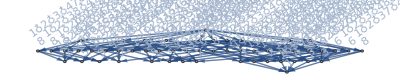
-Graphics-{{4,1},{5,51},{6,201},{7,132},{8,18}}

```mathematica
CountOfImplies[MinimalGraph[7]]
```

{v1x2x3x4567,v1x2x3x4567,v1x2x3x4567}→{}

{v1x2x34x567}→{}

{v1x2x3x45x67,v1x2x3x45x67,v1x23x4x5x67,v1x23x4x5x67,v1x23x45x6x7,v1x23x45x6x7}→{v1x23x45x67}

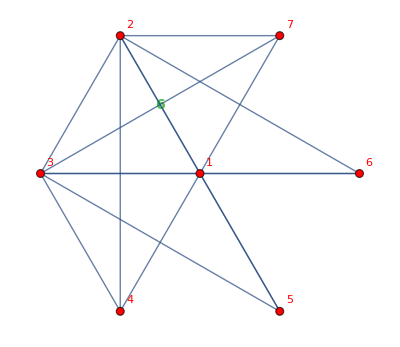
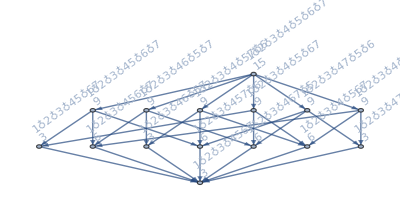
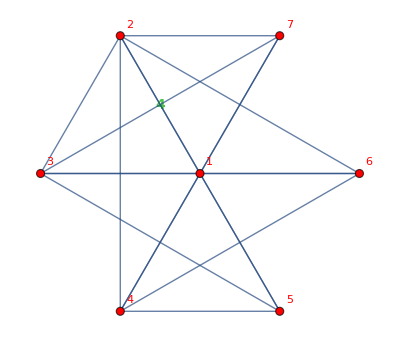
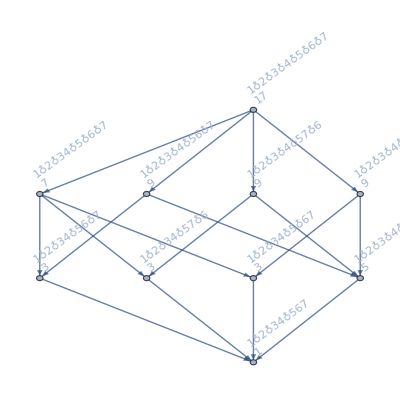
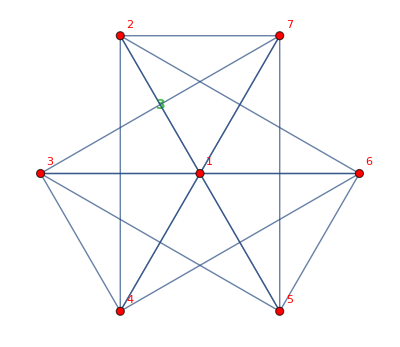
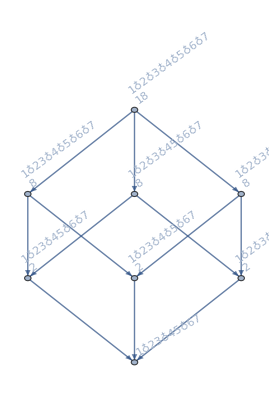
{-Graphics-→-Graphics-{{4,3},{5,33},{6,54},{7,15}},-Graphics-→-Graphics-{{4,1},{5,14},{6,34},{7,17}},-Graphics-→-Graphics-{{5,6},{6,24},{7,18}}}

```mathematica
Map[#->CountOfImplies[#]&,BarelyFourColorableGraphsOfCount[7]]
```

```mathematica
CountOfImplies[-Graphics-]
```

-Graphics-

{v1x2x3x45678,v1x2x3x45678,v1x2x3x45678}→{}

{v1x2x34x5678}→{}

{v1x2x345x678}→{}

{v1x2x3x45x678,v1x2x3x45x678,v1x23x4x5x678,v1x23x4x5x678,v1x23x45x6x78,v1x23x45x68x7,v1x23x45x67x8}→{v1x23x45x678}

{v1x2x3x4x56x78,v1x2x3x4x56x78,v1x2x34x5x6x78,v1x2x34x5x6x78,v1x2x34x56x7x8,v1x2x34x56x7x8,v1x2x3x4x56x78,v1x2x3x4x56x78,v1x2x34x5x6x78,v1x2x34x5x6x78,v1x2x34x56x7x8,v1x2x34x56x7x8,v12x3x4x5x6x78,v12x3x4x5x6x78,v12x3x4x56x7x8,v12x3x4x56x7x8,v12x3x4x5x6x78,v12x3x4x5x6x78,v12x3x4x56x7x8,v12x3x4x56x7x8,v12x34x5x6x7x8,v12x34x5x6x7x8,v12x34x5x6x7x8,v12x34x5x6x7x8}→{v12x3x4x56x78,v1x2x34x56x78,v12x34x5x6x78,v12x34x56x7x8,v12x34x56x78}

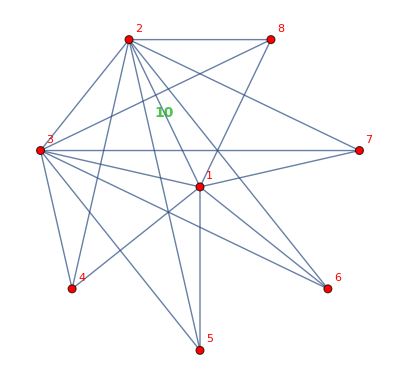
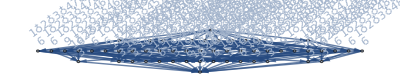
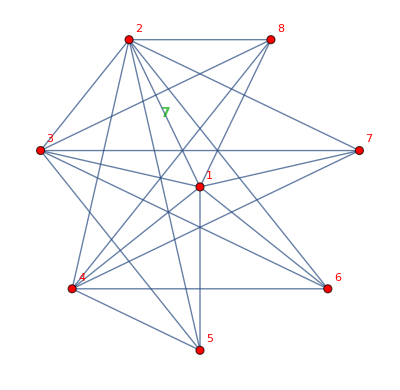
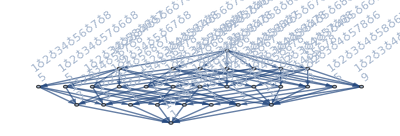
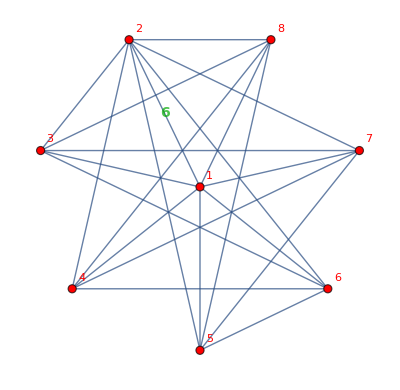
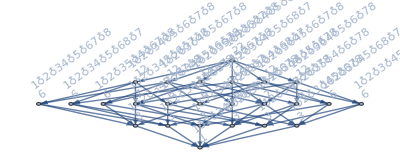
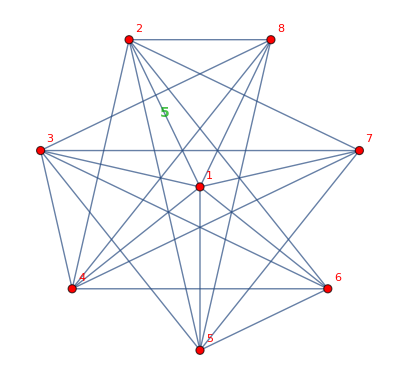
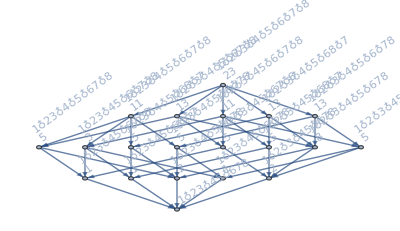
{-Graphics-→-Graphics-{{4,3},{5,60},{6,180},{7,120},{8,18}},-Graphics-→-Graphics-{{4,1},{5,20},{6,81},{7,87},{8,21}},-Graphics-→-Graphics-{{4,1},{5,18},{6,68},{7,72},{8,22}},-Graphics-→-Graphics-{{5,7},{6,41},{7,61},{8,23}},-Graphics-→-Graphics-{{6,24},{7,48},{8,24}}}

```mathematica
Map[#->CountOfImplies[#]&,BarelyFourColorableGraphsOfCount[8]]
```

```mathematica
Map[Last,{{4,3},{5,33},{6,54},{7,15}}]
```

{3,33,54,15}

```mathematica
Map[FactorInteger,%]
```

{{{3,1}},{{3,1},{11,1}},{{2,1},{3,3}},{{3,1},{5,1}}}

```mathematica
PrimeQ[87]
```

False

{v1x2x3x456789,v1x2x3x456789,v1x2x3x456789}→{}

{v1x2x34x56789}→{}

{v1x2x345x6789}→{}

{v1x2x3x45x6789,v1x2x3x45x6789,v1x23x4x5x6789,v1x23x4x5x6789,v1x23x45x6x789,v1x23x45x689x7,v1x23x45x679x8,v1x23x45x678x9}→{}

{v1x2x3x456x789,v1x2x3x456x789,v1x23x4x56x789,v1x23x46x5x789,v1x23x45x6x789,v1x23x456x7x89,v1x23x456x79x8,v1x23x456x78x9}→{v1x23x456x789}

{v1x2x3x4x56x789,v1x2x3x4x56x789,v1x2x34x5x6x789,v1x2x34x5x6x789,v1x2x34x56x7x89,v1x2x34x56x79x8,v1x2x34x56x78x9,v1x2x3x4x56x789,v1x2x3x4x56x789,v1x2x34x5x6x789,v1x2x34x5x6x789,v1x2x34x56x7x89,v1x2x34x56x79x8,v1x2x34x56x78x9,v12x3x4x5x6x789,v12x3x4x5x6x789,v12x3x4x56x7x89,v12x3x4x56x79x8,v12x3x4x56x78x9,v12x3x4x5x6x789,v12x3x4x5x6x789,v12x3x4x56x7x89,v12x3x4x56x79x8,v12x3x4x56x78x9,v12x34x5x6x7x89,v12x34x5x6x79x8,v12x34x5x6x78x9,v12x34x5x6x7x89,v12x34x5x6x79x8,v12x34x5x6x78x9}→{v12x3x4x56x789,v1x2x34x56x789,v12x34x5x6x789}

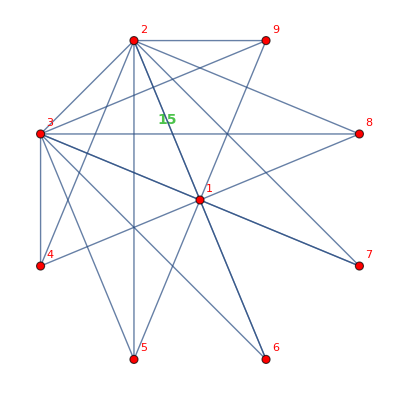
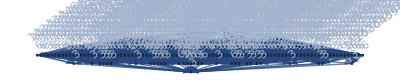
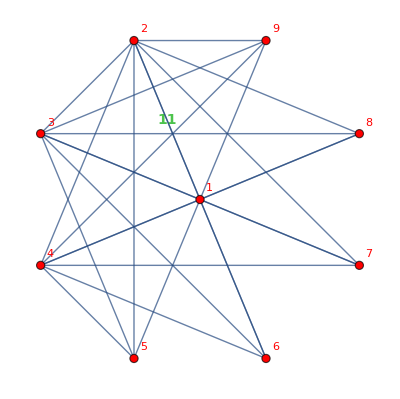
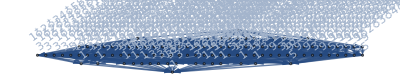
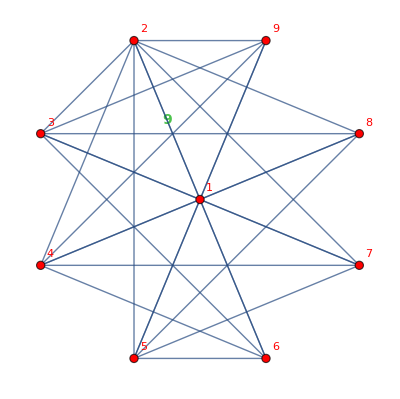
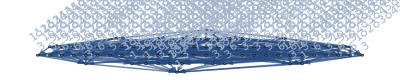
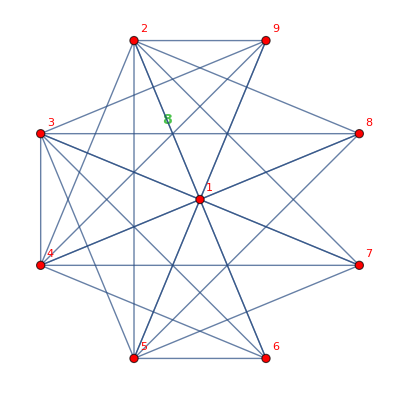
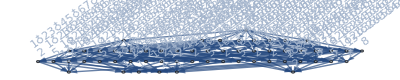
{-Graphics-→-Graphics-{{4,3},{5,111},{6,540},{7,645},{8,225},{9,21}},-Graphics-→-Graphics-{{4,1},{5,30},{6,190},{7,335},{8,181},{9,25}},-Graphics-→-Graphics-{{4,1},{5,24},{6,136},{7,240},{8,147},{9,27}},-Graphics-→-Graphics-{{5,8},{6,72},{7,176},{8,136},{9,28}},-Graphics-→-Graphics-{{5,8},{6,63},{7,145},{8,117},{9,29}},-Graphics-→-Graphics-{{6,30},{7,102},{8,102},{9,30}}}

```mathematica
Map[#->CountOfImplies[#]&,BarelyFourColorableGraphsOfCount[9]]
```

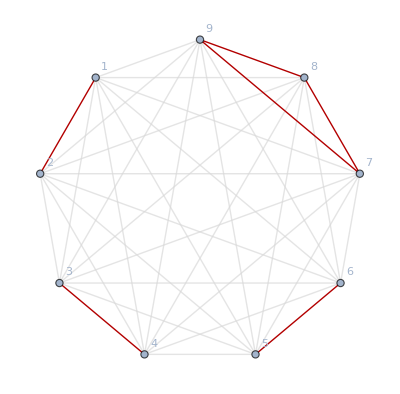

```mathematica
With[{g=-Graphics-},
CompleteGraph[VertexCount[g],GraphHighlight->EdgeList[GraphComplement[g]], GraphHighlightStyle->"Thick", VertexLabels->"Name", EdgeStyle->LightGray]
]
```

```mathematica
CountOfImplies[-Graphics-]
```

{v1x2x3x4x56x789,v1x2x3x4x56x789,v1x2x34x5x6x789,v1x2x34x5x6x789,v1x2x34x56x7x89,v1x2x34x56x79x8,v1x2x34x56x78x9,v1x2x3x4x56x789,v1x2x3x4x56x789,v1x2x34x5x6x789,v1x2x34x5x6x789,v1x2x34x56x7x89,v1x2x34x56x79x8,v1x2x34x56x78x9,v12x3x4x5x6x789,v12x3x4x5x6x789,v12x3x4x56x7x89,v12x3x4x56x79x8,v12x3x4x56x78x9,v12x3x4x5x6x789,v12x3x4x5x6x789,v12x3x4x56x7x89,v12x3x4x56x79x8,v12x3x4x56x78x9,v12x34x5x6x7x89,v12x34x5x6x79x8,v12x34x5x6x78x9,v12x34x5x6x7x89,v12x34x5x6x79x8,v12x34x5x6x78x9}→{v12x3x4x56x789,v1x2x34x56x789,v12x34x5x6x789}

-Graphics-{{6,30},{7,102},{8,102},{9,30}}

```mathematica
CommonDownWards[{v12x3x4x56x789,v1x2x34x56x789,v12x34x5x6x789}]
```

{}

```mathematica
FindFullFormula[-Graphics-]
```

{v1x2x3x4x5x6x7x8x9,v1x2x3x4x5x6x7x89,v1x2x3x4x5x6x79x8,v1x2x3x4x5x6x78x9,v1x2x3x4x5x6x789,v1x2x3x4x56x7x8x9,v1x2x3x4x56x7x89,v1x2x3x4x56x79x8,v1x2x3x4x56x78x9,v1x2x3x4x56x789,v1x2x34x5x6x7x8x9,v1x2x34x5x6x7x89,v1x2x34x5x6x79x8,v1x2x34x5x6x78x9,v1x2x34x5x6x789,v1x2x34x56x7x8x9,v1x2x34x56x7x89,v1x2x34x56x79x8,v1x2x34x56x78x9,v1x2x34x56x789,v12x3x4x5x6x7x8x9,v12x3x4x5x6x7x89,v12x3x4x5x6x79x8,v12x3x4x5x6x78x9,v12x3x4x5x6x789,v12x3x4x56x7x8x9,v12x3x4x56x7x89,v12x3x4x56x79x8,v12x3x4x56x78x9,v12x3x4x56x789,v12x34x5x6x7x8x9,v12x34x5x6x7x89,v12x34x5x6x79x8,v12x34x5x6x78x9,v12x34x5x6x789,v12x34x56x7x8x9,v12x34x56x7x89,v12x34x56x79x8,v12x34x56x78x9,v12x34x56x789}

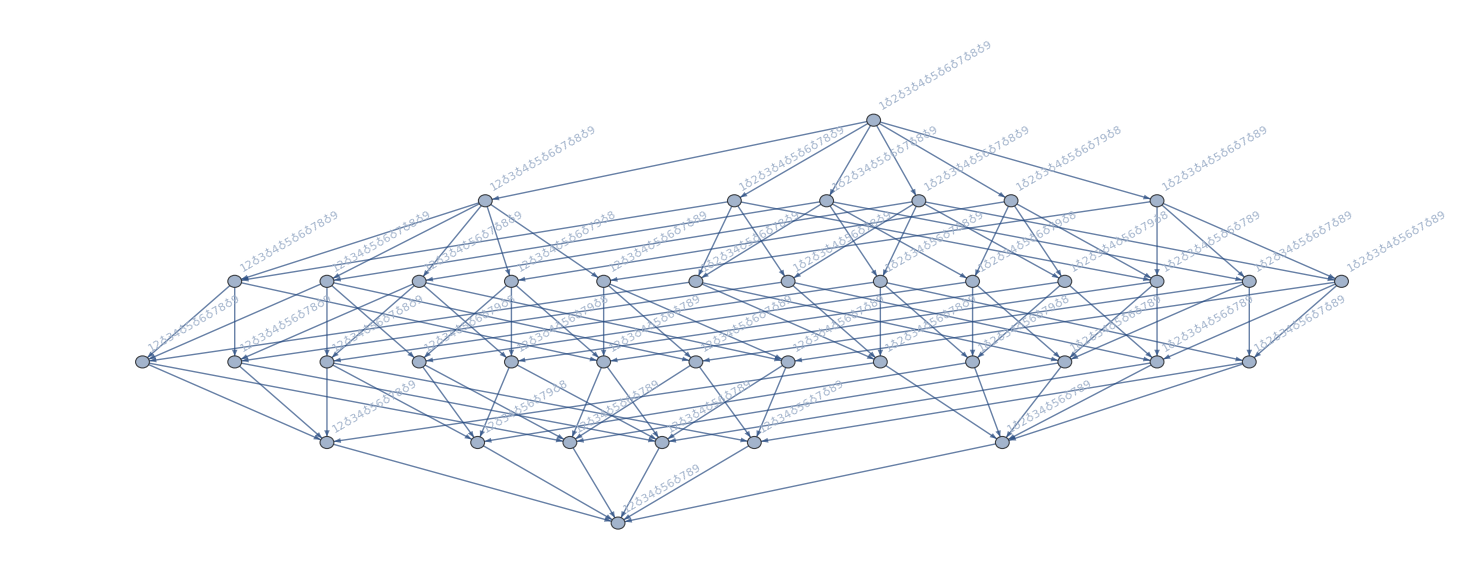

```mathematica
FormulaGraphReverse2[{v1x2x3x4x5x6x7x8x9,v1x2x3x4x5x6x7x89,v1x2x3x4x5x6x79x8,v1x2x3x4x5x6x78x9,v1x2x3x4x5x6x789,v1x2x3x4x56x7x8x9,v1x2x3x4x56x7x89,v1x2x3x4x56x79x8,v1x2x3x4x56x78x9,v1x2x3x4x56x789,v1x2x34x5x6x7x8x9,v1x2x34x5x6x7x89,v1x2x34x5x6x79x8,v1x2x34x5x6x78x9,v1x2x34x5x6x789,v1x2x34x56x7x8x9,v1x2x34x56x7x89,v1x2x34x56x79x8,v1x2x34x56x78x9,v1x2x34x56x789,v12x3x4x5x6x7x8x9,v12x3x4x5x6x7x89,v12x3x4x5x6x79x8,v12x3x4x5x6x78x9,v12x3x4x5x6x789,v12x3x4x56x7x8x9,v12x3x4x56x7x89,v12x3x4x56x79x8,v12x3x4x56x78x9,v12x3x4x56x789,v12x34x5x6x7x8x9,v12x34x5x6x7x89,v12x34x5x6x79x8,v12x34x5x6x78x9,v12x34x5x6x789,v12x34x56x7x8x9,v12x34x56x7x89,v12x34x56x79x8,v12x34x56x78x9,v12x34x56x789}]
```